# Практикум №1. Приемы работы в Mathematica

Вариант 8. Выполнила студентка ММФ БГУ
КМ, 1 к, 5 гр. Шклярик В.С.
  2 сентября 2021

## 2. Ввод и отображение математических комбинаций

### Задание 2.1

Введите с клавиатуры выражение y(x)

```mathematica
1/(2 √(a b))×Log[(√a+x*√b)/(√a-x*√b)]
```

Log[(√a+√b x)/(√a-√b x)]/(2 √(a b))

### Задание 2.2

Ознакомьтесь с различными форматами представления выражения. 
Используйте выражение y(x), введенное при выполнении задания 2.1.

```mathematica
Log[(√a+√b x)/(√a-√b x)]/(2 √(a b))//FullForm
```

Times[Rational[1,2],Power[Times[a,b],Rational[-1,2]],Log[Times[Power[Plus[Power[a,Rational[1,2]],Times[-1,Power[b,Rational[1,2]],x]],-1],Plus[Power[a,Rational[1,2]],Times[Power[b,Rational[1,2]],x]]]]]

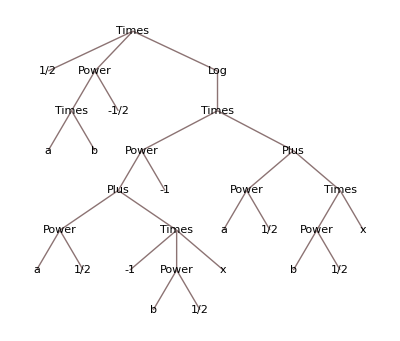

```mathematica
Log[(√a+√b x)/(√a-√b x)]/(2 √(a b))//TreeForm
```

Для того, чтобы построить полную форму выражения, нужно  привести выражение в StandartForm с помощью комбинаций клавиш Ctrl+Shift+N. Используя постфиксную форму записи функции //FullForm, получить полную форму выражения: y (x) //FullForm.

### Задание 2.3

Для выражения y(x), введенного при выполнении задания 2.1, вычислите 
его производную по переменной x и упростите ее. Используйте функции 
семейства Simplify.

```mathematica
D[1/(2 √(a b))×Log[(√a+x*√b)/(√a-x*√b)],x]
```

((√a-√b x) ((√b)/(√a-√b x)+(√b (√a+√b x))/(√a-√b x)^2))/(2 √(a b) (√a+√b x))

```mathematica
FullSimplify[((√a-√b x) ((√b)/(√a-√b x)+(√b (√a+√b x))/(√a-√b x)^2))/(2 √(a b) (√a+√b x)), a>0;b>0]
```

1/(a-b x^2)

```mathematica
myExpr=1/(a-b x^2)
```

1/(a-b x^2)

```mathematica
?myExpr
```

## 3. Работа с системой справки

### Задание 3.1

В заданном квадратном трехчлене, выражении вида a x2 + b x + c, a≠0, 
выделите полный квадрат относительно переменной x, введя подходящую 
замену переменных. 
Результат вычисления ассоциируйте с символом Result.

```mathematica
Result=67*x^2-105*x-172/.x->(k+105/2)/67 //Simplify
```

1/268 (-57121+4 k^2)

```mathematica
?Result
```

### Задание 3.2

```mathematica
Factor[Result]
```

1/268 (-239+2 k) (239+2 k)

```mathematica
ResProduct=Length[1/268 (-239+2 k) (239+2 k)]
```

3

Полученное количество множителей=3

```mathematica
Expand[Result]
```

-57121/268+k^2/67

```mathematica
ResSum=Length[-57121/268+k^2/67]
```

2

Полученное количество слагаемых=2

### Задание 3.3

Integer- целое число без десятичной точки, Real- вещественное число, состоящее из целой и дробной части числа, а также десятичной точки. При практическом использовании не стоит изменять тип атомарного объекта, не изменяя при этом его значения.

```mathematica
Head[67]
```

Integer

```mathematica
Head[67.0]
```

Real

```mathematica
ResultReal=67*x^2-105*x-172/.x->(k+105/2)/67. //Simplify
```

-213.138+0.0149254 k^2

```mathematica
67.0*x^(2.0)-105.0*x-172.0/.x->(k+52.5)/67.0//Simplify
```

-254.276-1.56716 k+0.0149254 (52.5+k)^2.

### Задание 3.4

```mathematica
Quadratic[expr:a_.x^2+b_.x+c_.]:= expr/. x->(k-b/2)/a//Simplify
```

```mathematica
Quadratic[67*x^2-105*x-172]
```

1/268 (-57121+4 k^2)

Созданная мной функция Quadratic работает правильно, результат совпадает с Result

### Задание 3.5

```mathematica
Plot[67*x^2-105*x-172,{x,-100,100},PlotStyle->Pink,PlotTheme->"Monochrome", PlotLabels->"Expressions",Filling->Axis,Axes->True, AxesStyle->Directive[Orange, 5]]
```

-Graphics-

## 4. Решение уравнений, неравенств и их систем

### Задание 4.1

Решите заданную систему уравнений несколькими способами, используя: 
1) возможности графики, 
2) встроенные функции для решения систем уравнений.

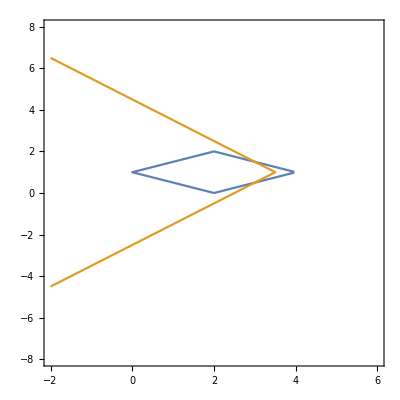

```mathematica
ContourPlot[{Abs[x-2]+2*Abs[y-1]==2,x+Abs[y-1]==3.5},{x,-2,6},{y,-8,8}]
```

```mathematica
Solve[{Abs[x-2]+2*Abs[y-1]==2,x+Abs[y-1]==3.5}]
```

{{x→3.,y→0.5},{x→3.,y→1.5}}

```mathematica
Reduce[Abs[x-2]+2*Abs[y-1]==2&&x+Abs[y-1]==3.5,{x,y},Reals]
```

(x==3.&&y==0.5)||(x==3.&&y==1.5)

(x; y)=(3; 1,5),(3; 0,5)

### Задание 4.2

Решите заданное уравнение относительно переменной x, при условии, что 
вторая переменная является вещественным параметром. Используйте 
функции Solve и Reduce. Сформулируйте выводы об использовании этих 
функций.

```mathematica
Solve[(x^2-5*x+4)/(x-a)==0,x]
```

{{x→1},{x→4}}

```mathematica
Reduce[(x^2-5*x+4)/(x-a)==0,x]
```

(x==1&&-1+a≠0)||(x==4&&-4+a≠0)

Обе функции решают уравнение, но Reduce также указывает область допустимых значений для параметра а.

(x^2-5*x+4)/(x-a)=0
x≠a
x^2-5*x+4=0
(x-1)*(x-4)=0
x=4 или х=1 при 1≠а, 4≠a

### Задание 4.3

Продемонстрируйте графически зависимость решения уравнения (задание 4.2)  от значений параметра.

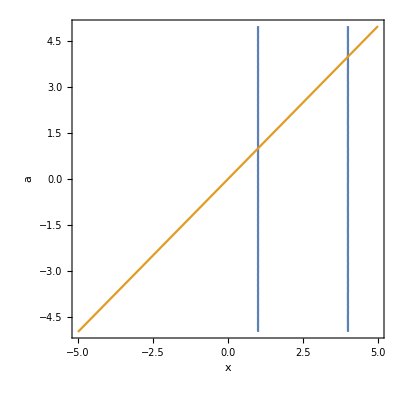

```mathematica
ContourPlot[{x^2-5*x+4==0, x-a==0},{x,-5,5},{a,-5,5},Axes->True, AxesLabel->{x,a}]
```

Ответ: при а ≠ 1&&a≠4 x_1 =1||x_2 =4,  при a=1 х_1=4, при a=4 x_1=1

```mathematica
Reduce[(x^2-5*x+4)/(x-a)==0,x]
```

(x==1&&-1+a≠0)||(x==4&&-4+a≠0)

### Задание 4.4

Решите заданное неравенство относительно переменной x, при условии, что 
вторая переменная является вещественным параметром. Используйте 
функции Solve и Reduce. Сформулируйте выводы об использовании этих 
функций.

```mathematica
Solve[Abs[x-2]<=a,x,Reals]
```

Solve::fdimc: When parameter values satisfy the condition a>0, the solution set contains a full-dimensional component; use Reduce for complete solution information.

{}

```mathematica
Reduce[Abs[x-2]≤a,x, Reals]
```

(a==0&&x==2)||(a>0&&2-a≤x≤2+a)

Reduce,  в отличие от Solve может решать неравенства с параметром.

### Задание 4.5

Продемонстрируйте графически зависимость решения неравенства (задание 
4.3) от значений параметра. Запишите ответ при каждом значении параметра.

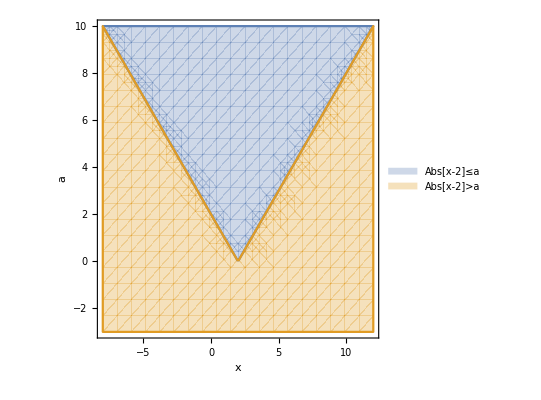

```mathematica
RegionPlot[{Abs[x-2]<=a,Abs[x-2]>a}, {x,-8,12},{a,-3,10},Axes->True, PlotLegends->"Expressions",AxesLabel->Automatic]
```

Визуализация геометрической области RegionPlot демонстрирует зависимость решений неравенства от значения параметра.  При а=0   х=2,  при а>0    2-a ≤ x ≤ 2+a.

## 5. Закрепление навыков и умений

Reduce, Solve, Abs,Manipulate,Factor,Expand, Simplify, FullForm,TreeForm